```mathematica
x[x_] := x^2
```

```mathematica
x[2]
```

4

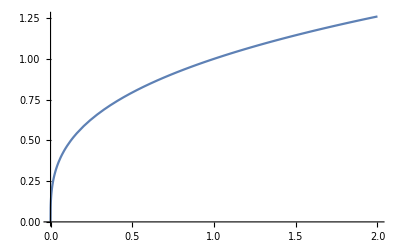

```mathematica
line2 = Plot[x^(1/3), {x, 0, 2}]
```

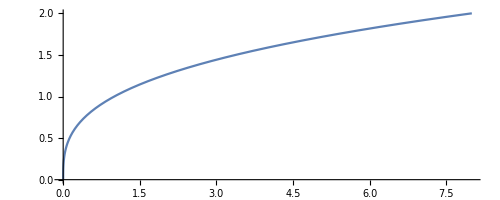

```mathematica
line = ParametricPlot[{t^3, t}, {t, 0, 2}]
```

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],z (2+Sin[t] Cos[t]^2)},{t,0,π/2},{z,0,1},MeshFunctions->{#2&},MeshStyle->{Red},BoundaryStyle->Directive[Thick,Blue],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{Cos[t],Sin[t],2+Sin[t] Cos[t]^2},{t,0,π,0.01}],Filling->0]
```

-Graphics3D-

```mathematica
lineintegral = ListPointPlot3D[Table[{t^3,t,t^3},{t,0,2,0.01}],Filling->0]
```

-Graphics3D-

```mathematica
test1  = ListPointPlot3D[Table[{4Cos[t],4Sin[t],1024Cos[t] Sin[t]^4},{t,0,π,0.01}],Filling->0]
```

-Graphics3D-

```mathematica
ParametricPlot[{4Cos[t], 4Sin[t]}, {t,0,π,}]
```

ParametricPlot::plln: Limiting value Null in {t,0,π,Null} is not a machine-sized real number.

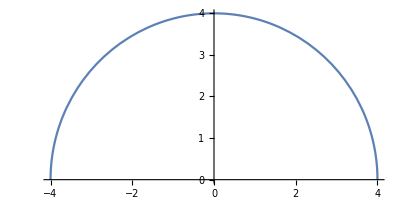

```mathematica
test2 = ParametricPlot[{4 Cos[t],4 Sin[t]},{t,0,π}]
```

```mathematica
ListPointPlot3D[Table[{t,2t,t*Exp[2t]},{t,0,1,0.01}],Filling->0]
```

-Graphics3D-

Show::gcomb: Could not combine the graphics objects in Show[,].

{4 y^3,-2 x^2}

-Graphics-

-Graphics-

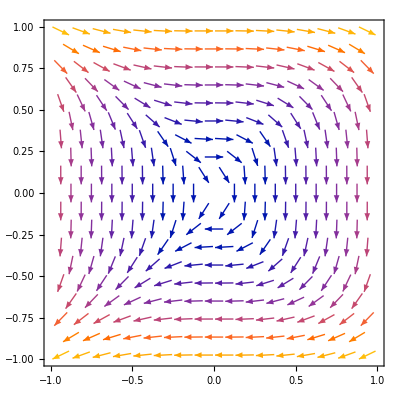

```mathematica
F={4 y^3,-2 x^2}
p=VectorPlot[F,{x,-1,1},{y,-1,1}];

c=Graphics[{EdgeForm[Thick],Transparent,Rectangle[{-1,-1},{1,1}]}]
c
Show[p,c]
```

```mathematica
ListPointPlot3D[Table[{t^3,t,t^3},{t,0,2,0.01}],Filling->0]
```

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],z (2+Sin[t] Cos[t]^2)},{t,0,π/2},{z,0,1},MeshFunctions->{#2&},MeshStyle->{Red},BoundaryStyle->Directive[Thick,Blue],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t], Sin[t], z (2 + Sin[t] Cos[t]^2)}, {t, 
  0, π/2}, {z, 0, 1}, MeshFunctions -> {#2 &}, MeshStyle -> {RGBColor[0.34,0.31,0.55]}, ColorFunction->"DarkRainbow",
  BoundaryStyle -> Directive[Thin, RGBColor[0, 0.24, 0.36]], BoxRatios -> {1, 1, 1/2}, 
 PlotStyle -> Opacity[.8]]
```

-Graphics3D-